LevelScheme examples

M. A. Caprio, Department of Physics, University of Notre Dame

## Package initialization

If you have not already loaded the LevelScheme package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["LevelScheme`"];
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.51 (February 23, 2011)
View color paletteVisit home page  -Graphics-

## First example from User's Guide

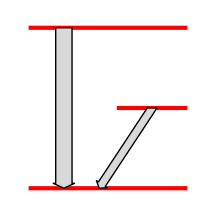

```mathematica
Figure[
{
SetOptions[Lev,Thickness->3,Color->Red],
SetOptions[Trans,ArrowType->ShapeArrow,FillColor->LightGray],
Lev[lev1,0,2,0],
Lev[lev2,1,2,100],
Lev[lev3,0,2,200],
Trans[lev2,0.5,lev1,0.9,Width->10],
Trans[lev3,0.5,lev1,0.5,Width->20]
},
PlotRange->{{0,2},{-10,210}}, ImageSize->72*{3,3}
]
```

## Another simple level scheme

Notice the use of Table and formulas to calculate the level energies.  This example also illustrates the alternate syntax for labeling levels (with Tag) and specifying transition arrow endpoint placement (with EndPositions).

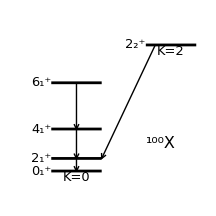

```mathematica
Figure[
{

SetOptions[SchemeObject,FontSize->13],
SetOptions[Lev,OffsetL->{+1,0},OffsetR->{-1,0},Thickness->2],

(* bands *)
Table[
Lev[0,1,J*(J+1)/6*100,LabL->LabelJiP[J,1],Tag->lev[J,1]],
{J,0,6,2}
],

SetOrigin[1.5],
Lev[0,1,1000,LabL->LabelJiP[2,2],Tag->lev[2,2]],
SetOrigin[],

BandLabel[lev[0,1],"K=0"],
BandLabel[lev[2,2],"K=2"],

(* transitions *)
Table[
Trans[lev[J,1],lev[J-2,1]],
{J,2,6,2}
],
Trans[lev[2,2],lev[2,1],EndPositions->{0.25,0.9}],

(* panel label *)
ScaledLabel[{0.8,0.3},Isotope[100,"X"],FontSize->16]

},
PlotRange->{{0,2},{0,1000}},
ExtendRange->0.2,
ImageSize->72*{3,3}
]
```

## Simple two-panel level scheme

Adapted from M. A. Caprio, Ph.D. thesis, Yale University (2003), arXiv:nucl-ex/0502004.

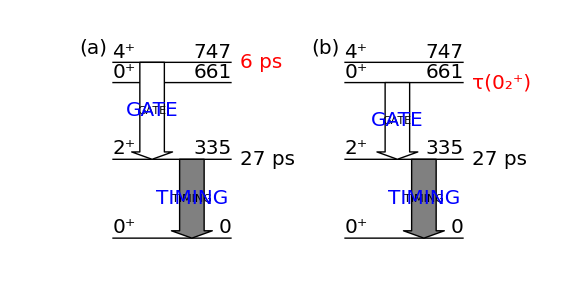

```mathematica
Figure[{

(* set default styles for level scheme objects *)

SetOptions[SchemeObject,FontSize->20];
SetOptions[Lev,NudgeL->1,NudgeR->1,LabR->Automatic],
SetOptions[Trans,ArrowType->ShapeArrow,HeadLength->9,HeadLip->10,Width->30,
FontColor->Blue,OrientationC->Horizontal,BackgroundC->Automatic],
SetOptions[LevelLabel,Gap->10],

(* draw cascade from 4+ level *)

SetOrigin[0],
ManualLabel[{-.4,850},"(a)",Offset->{-1,1}],

Lev[lev0,0,2,"0",LabL->LabelJP[0]],
Lev[lev335,0,2,"335",LabL->LabelJP[2]],
LevelLabel[lev335,Right,"27 ps"],
Lev[lev661,0,2,"661",LabL->LabelJP[0]],
Lev[lev747,0,2,"747",LabL->LabelJP[4]],
LevelLabel[lev747,Right,"  6 ps",FontColor->Red],
Trans[lev335,1.3,lev0,Automatic,FillColor->Gray,LabC->"TIMING"],
Trans[lev747,.7,lev335,Automatic,FillColor->White,LabC->"GATE"],

(* draw cascade from 0+ level *)

SetOrigin[3.5],
ManualLabel[{-.4,850},"(b)",Offset->{-1,1}],

Lev[lev0,0,2,"0",LabL->LabelJP[0]],
Lev[lev335,0,2,"335",LabL->LabelJP[2]],
LevelLabel[lev335,Right,"27 ps"],
Lev[lev661,0,2,"661",LabL->LabelJP[0]],
LevelLabel[lev661,Right,Row[{"τ(",hspace[-0.2],LabelJiP[0,2],")"}],FontColor->Red],
Lev[lev747,0,2,"747",LabL->LabelJP[4]],
Trans[lev335,1.3,lev0,Automatic,FillColor->Gray,LabC->"TIMING"],
Trans[lev661,.9,lev335,Automatic,FillColor->White,LabC->"GATE"],

},
PlotRange->{{-.8,6.3},{-100,900}},ImageSize->72*{8,4}
]
```

## Level scheme combining various styles of transition arrow

Adapted from M. A. Caprio, Ph.D. thesis, Yale University (2003), arXiv:nucl-ex/0502004.

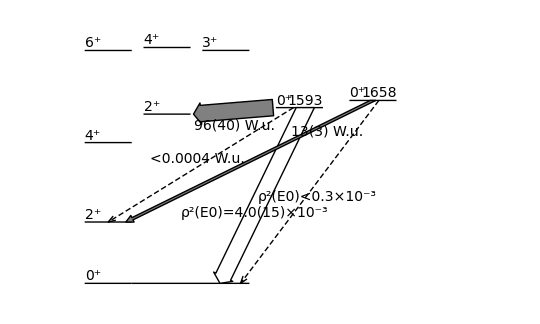

```mathematica
Figure[{
SetOptions[SchemeObject,FontSize->14],
SetOptions[Trans,HeadLength->9, HeadLip->3,ArrowType->ShapeArrow],

Lev[lev100,0,1,0,LabL->LabelJP[0]],
Lev[lev112,0,1,556,LabL->LabelJP[2]],
Lev[lev124,0,1,1276,LabL->LabelJP[4]],
Lev[lev122,1,2,1534,LabL->LabelJP[2]],

Lev[lev136,0,1,2110.9,LabL->LabelJP[6]],
Lev[lev134,1,2,2138,LabL->LabelJP[4]],
Lev[lev133,2,3,2111.5,LabL->LabelJP[3]],

SetOrigin[3.25],
Lev[lev01,0,1,1593,LabL->LabelJP[0],LabR->Automatic],
ExtensionLine[lev100,Right,2],
Trans[lev01,.6,lev100,2.4,Width->20,FillColor->White,LabC->\(ρ\^2(\*textit["E"]0)=4.0(15)×10\^-3\),PosnC->0.6],
Trans[lev01,.4,lev112,.5,ArrowType->LineArrow,Dashing->Automatic,LabL->"<0.0004 W.u."],
Trans[lev01,.05,lev122,.95,TailBevel->False,Width->20,FillColor->Gray,LabR->"96(40) W.u."],

SetOrigin[4.5],
Lev[lev02,0,1,1658,LabL->LabelJP[0],LabR->Automatic],
Trans[lev02,0.5,lev112,0.8,Width->3,FillColor->Gray,LabR->"13(3) W.u.",PosnR->0.2],
Trans[lev02,0.6,lev100,2.75,ArrowType->LineArrow,Dashing->Automatic,LabR->\(ρ\^2(\*textit["E"]0)<0.3×10\^-3\),BufferR->1.5],

},PlotRange->{{-0.5,7},{-100,2300}},Frame->False,ImageSize->72*{7.5,4.5}]
```

## Level scheme with bent arrows

Adapted from M. A. Caprio, Ph.D. thesis, Yale University (2003), arXiv:nucl-ex/0502004.

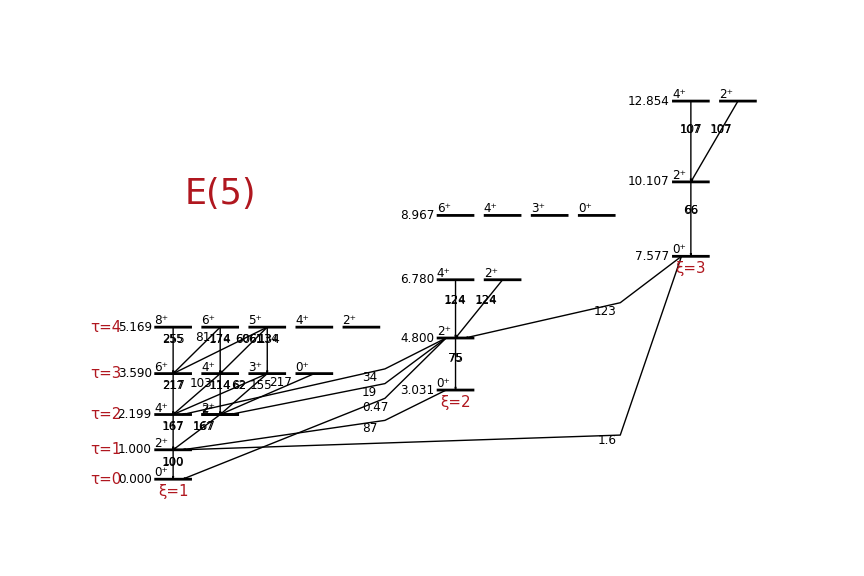

```mathematica
a=6;  (* first interfamily horizontal separation *)
b=5; (* second interfamily horizontal separation *)
d=0.2;  (* arrow position parameter for kinked arrows *)
Figure[{

SetOptions[Lev,Thickness->2],
SetOptions[Trans,Thickness->1,
HeadLength->4,HeadLip->0.5,
PosnC->FromTailVertical[15],BackgroundC->Automatic,OrientationC->Horizontal,
PosnL->FromTailVertical[17],BufferL->1.0,
PosnR->FromTailVertical[10],BufferR->1.0
],
SetOptions[LevelLabel,Gap->3],
 
ScaledLabel[{0.2,0.7},"E(5)",FontSize->35,Color->IndianRed],

(* ξ=1 *)

Lev[lev100,0,1,"0.000",LabL->LabelJP[0]],
LevelLabel[lev100,Left,"0.000"],
Lev[lev112,0,1,"1.000",LabL->LabelJP[2]],
LevelLabel[lev112,Left,"1.000"],
Lev[lev124,0,1,"2.199",LabL->LabelJP[4]],
Lev[lev122,1,2,"2.199",LabL->LabelJP[2],BackgroundL->Automatic],  (* background for crossover arrow *)
Lev[lev122redraw,1,2,"2.199",Layer->5],  (* inelegant fix so background label doesn't hide line *)
LevelLabel[lev124,Left,"2.199"],
Lev[lev136,0,1,"3.590",LabL->LabelJP[6]],
Lev[lev134,1,2,"3.590",LabL->LabelJP[4]],
Lev[lev133,2,3,"3.590",LabL->LabelJP[3]],
Lev[lev130,3,4,"3.590",LabL->LabelJP[0]],
LevelLabel[lev136,Left,"3.590"],
Lev[lev148,0,1,"5.169",LabL->LabelJP[8]],
Lev[lev146,1,2,"5.169",LabL->LabelJP[6]],
Lev[lev145,2,3,"5.169",LabL->LabelJP[5]],
Lev[lev144,3,4,"5.169",LabL->LabelJP[4]],
Lev[lev142,4,5,"5.169",LabL->LabelJP[2]],
LevelLabel[lev148,Left,"5.169"],

Trans[lev112,0.5,lev100,0.5,LabC->"100"],
Trans[lev124,0.5,lev112,0.5,LabC->"167"],
Trans[lev122,0.5,lev112,0.5,LabC->"167"],
Trans[lev136,0.5,lev124,0.5,LabC->"217"],
Trans[lev134,0.5,lev124,0.5,LabL->"103"],
Trans[lev134,0.5,lev122,0.5,LabC->"114"],
Trans[lev133,0.5,lev124,0.5,LabC->"62",LabC->"62.0"],(*LabL->"62",PosnL->FromTailVertical[12],*)
Trans[lev133,0.5,lev122,0.5,LabR->"155"],
Trans[lev130,0.5,lev122,0.5,LabL->"217"],
Trans[lev148,0.5,lev136,0.5,LabC->"255"],
Trans[lev146,0.5,lev136,0.5,LabL->"81",LabL->"81.2"],
Trans[lev146,0.5,lev134,0.5,LabC->"174"],
Trans[lev145,0.5,lev136,0.5,LabC->"60",LabC->"60.3"],
Trans[lev145,0.5,lev134,0.5,LabC->"61",LabC->"60.9",NudgeC->{1.2,0}],
Trans[lev145,0.5,lev133,0.5,LabC->"134",NudgeC->{1.8,0}],

(* ξ=2 *)

SetOptions[Trans,PosnC->FromTailVertical[25]],

SetOrigin[a];
Lev[lev200,0,1,"3.031",LabL->LabelJP[0]],
LevelLabel[lev200,Left,"3.031"],
Lev[lev212,0,1,"4.800",LabL->LabelJP[2]],
LevelLabel[lev212,Left,"4.800"],
Lev[lev224,0,1,"6.780",LabL->LabelJP[4]],
Lev[lev222,1,2,"6.780",LabL->LabelJP[2]],
LevelLabel[lev224,Left,"6.780"],
Lev[lev236,0,1,"8.967",LabL->LabelJP[6]],
Lev[lev234,1,2,"8.967",LabL->LabelJP[4]],
Lev[lev233,2,3,"8.967",LabL->LabelJP[3]],
Lev[lev230,3,4,"8.967",LabL->LabelJP[0]],
LevelLabel[lev236,Left,"8.967"],


Trans[lev212,0.5,lev200,0.5,LabC->"75"],
Trans[lev224,0.5,lev212,0.5,LabC->"124"],
Trans[lev222,0.5,lev212,0.5,LabC->"124"],

ekink=2;
dekink=0.5;
Trans[lev200,0.5-d,lev112,0.5+d,Kink->{-1,ekink},LabR->"87",PosnR->FromTailHorizontal[20]],
Trans[lev212,0.5-d,lev100,0.5+d,Kink->{-1,ekink+=1.5*dekink},LabR->"0.47",PosnR->FromTailHorizontal[20-6]],
Trans[lev212,0.5-d,lev122,0.5+d,Kink->{-1,ekink+=1*dekink},LabR->"19",PosnR->FromTailHorizontal[20]],
Trans[lev212,0.5-d,lev124,0.5+d,Kink->{-1,ekink+=1*dekink},LabR->"34",PosnR->FromTailHorizontal[20]],

(* ξ=3 *)

SetOptions[Trans,PosnC->FromTailVertical[35]],

SetOrigin[a+b];
Lev[lev300,0,1,"7.577",LabL->LabelJP[0]],
LevelLabel[lev300,Left,"7.577"],
Lev[lev312,0,1,"10.107",LabL->LabelJP[2]],
LevelLabel[lev312,Left,"10.107"],
Lev[lev324,0,1,"12.854",LabL->LabelJP[4]],
Lev[lev322,1,2,"12.854",LabL->LabelJP[2]],
LevelLabel[lev324,Left,"12.854"],

Trans[lev312,0.5,lev300,0.5,LabC->"66"],
Trans[lev324,0.5,lev312,0.5,LabC->"107"],
Trans[lev322,0.5,lev312,0.5,LabC->"107"],

Trans[lev300,0.5-d,lev112,0.5+d,Kink->{-1,1.5},LabR->"1.6",PosnR->FromTailHorizontal[20-4]],
Trans[lev300,0.5-d,lev212,0.5+d,Kink->{-1,6},LabR->"123",PosnR->FromTailHorizontal[20]],


(* τ and ξ labels *)

SetOptions[LevelLabel,Gap->40,Color->IndianRed,FontSize->15],
LevelLabel[lev100,Left,"τ=0"],
LevelLabel[lev112,Left,"τ=1"],
LevelLabel[lev124,Left,"τ=2"],
LevelLabel[lev136,Left,"τ=3"],
LevelLabel[lev148,Left,"τ=4"],

SetOptions[BandLabel,Nudge->-6,Color->IndianRed,FontSize->15],
BandLabel[lev100,"ξ=1"],
BandLabel[lev200,"ξ=2"],
BandLabel[lev300,"ξ=3"],

},
PlotRange->{{-1.5,a+b+2.5},{-1.5,14.5}},ImageSize->72*{12,8}
]
```

## Beta decay scheme

The LevelScheme layered drawing system is necessary to prevent the white-out boxes behind the labels from obstructing the neighboring labels.  To see what would happen if there were no layered drawing system, temporarily disable layering by including
	SetOptions[SchemeObject,Layer→0].
at the beginning of the scheme.

Adapted from E. A. McCutchan et al., Phys. Rev. C 71, 024309 (2005).
Courtesy of E. A. McCutchan.

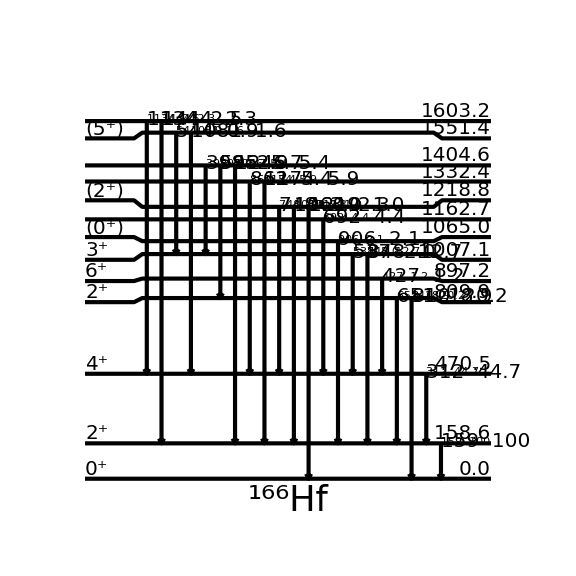

```mathematica
Figure[{

SetOptions[Trans,BackgroundT->Automatic,NudgeT->2, Thickness -> 3, FontSize -> 20, OrientationT -> Automatic],
SetOptions[Lev,Thickness->3,LabR->Automatic, FontSize -> 20, WingRiseWidth -> 10, WingTipWidth -> 60],

(* title *)
ManualLabel[{7,-100},"^166Hf", FontSize -> 35],

(* levels *)
Lev[lev0,0,14,"0.0", LabL -> "0^+"],
Lev[lev159,0,14,"158.6", LabL -> "2^+"],
Lev[lev470,0,14,"470.5", LabL -> "4^+"],
Lev[lev810,0,14,"809.9",WingHeight->-5, LabL -> "2^+"],
Lev[lev897, 0,14,"897.2",  LabL -> "6^+", WingHeight -> -3],
Lev[lev1006,0,14,"1007.1",WingHeight->-7,  LabL -> "3^+"],
Lev[lev1065,0,14,"1065.0", WingHeight -> +5,  LabL -> "(0^+)"],
Lev[lev1164,0,14,"1162.7"],
Lev[lev1219, 0, 14, "1218.8", WingHeight -> +8,  LabL -> "(2^+)"],
Lev[lev1332,0,14,"1332.4"],
Lev[lev1405, 0 ,14, "1404.6"],
Lev[lev1551, 0,14,"1551.4",  LabL -> "(5^+)", WingHeight  -> -7],
Lev[lev1603, 0,14, "1603.2"],

(* transitions *)
AutoLevelInit[12.2,-0.5,-0.5],
AutoLevel[lev159],
AutoTrans[lev0,LabT->"159  100"],

AutoLevel[lev470],
AutoTrans[lev159,LabT->"312  44.7"],

AutoLevel[lev810],
AutoTrans[lev0,LabT->"810  20.2"],
AutoTrans[lev159, LabT -> "651  18.9"],

AutoLevel[lev897],
AutoTrans[lev470, LabT -> "427  1.2"],

AutoLevel[lev1006],
AutoTrans[lev159, LabT -> "848  12.7"],
AutoTrans[lev470, LabT -> "537  2.0"],

AutoLevel[lev1065],
AutoTrans[lev159, LabT -> "906  2.1"],

AutoLevel[lev1164],
AutoTrans[lev470, LabT -> "692  4.4"],

AutoLevel[lev1219],
AutoTrans[lev0, LabT -> "1219  1.0"],
AutoTrans[lev159, LabT -> "1060  2.3"],
AutoTrans[lev470, LabT -> "748  3.0"],

AutoLevel[lev1332],
AutoTrans[lev159, LabT -> "1174  5.9"],
AutoTrans[lev470, LabT -> "862  5.4"],

AutoLevel[lev1405],
AutoTrans[lev159, LabT -> "1246  5.4"],
AutoTrans[lev810, LabT -> "595  5.7"],
AutoTrans[lev1006, LabT -> "398  2.9"],

AutoLevel[lev1551],
AutoTrans[lev470, LabT -> "1081  1.6"],
AutoTrans[lev1006, LabT -> "544  0.9"],

AutoLevel[lev1603],
AutoTrans[lev159, LabT -> "1444  2.3"],
AutoTrans[lev470, LabT -> "1134  2.5" ],


},
PlotRange->{{-1,15},{-200,1910}},
ImageSize->72*{8,8}
]
```

## Nuclear shell model diagram

Example of writing simple functions to automatically create the list of levels to plot, calcule the level energies, generate the labels, etc.

Labeling -- spectroscopic notation and color scheme for levels

```mathematica
SpectroscopicLetter[0]="s";
SpectroscopicLetter[1]="p";
SpectroscopicLetter[2]="d";
SpectroscopicLetter[3]="f";
SpectroscopicLetter[4]="g";
SpectroscopicLetter[5]="h";
SpectroscopicLetter[6]="i";
SpectroscopicLetter[7]="j";
SpectroscopicLetter[8]="k";
```

```mathematica
ShellLabel[{n_,l_,j_}]:=Row[{n,Subscript[SpectroscopicLetter[l],SolidusFractionize[j]]}];
ShellGrade[{n_,l_,j_}]:=Mod[2*n+l,2];
ShellColor[{n_,l_,j_}]:=Switch[ShellGrade[{n,l,j}],0,Blue,1,Red];
```

Energy function

```mathematica
ESM[{ho_,D_,xi_},{n_,l_,j_}]:=(2*n+l+3/2)*ho+D*l*(l+1)+1/2*xi*(+l*KroneckerDelta[j,l+1/2]-(l+1)*KroneckerDelta[j,l-1/2]);
```

Generating set of orbitals by major shell

```mathematica
LevelSetOrbital[N_]:=Table[{1/2*(N-l),l},{l,Mod[N,2],N,2}];
LevelSetSpinOrbit[NMax_]:=Module[
{n,l,j},
Last[Last[Reap[
Do[
{n,l}=nl;
j=l+sigma*1/2;
If[j>0,Sow[{n,l,j}]],
{N,0,NMax},{nl,LevelSetOrbital[N]},{sigma,{-1,+1}}
]
]]]
];
```

Specifically, levels through N=3 plus g9/2 orbit

```mathematica
PlotLevelSet=Append[
LevelSetSpinOrbit[3],
{0,4,9/2}
]
```

{{0,0,1/2},{0,1,1/2},{0,1,3/2},{1,0,1/2},{0,2,3/2},{0,2,5/2},{1,1,1/2},{1,1,3/2},{0,3,5/2},{0,3,7/2},{0,4,9/2}}

Make plot

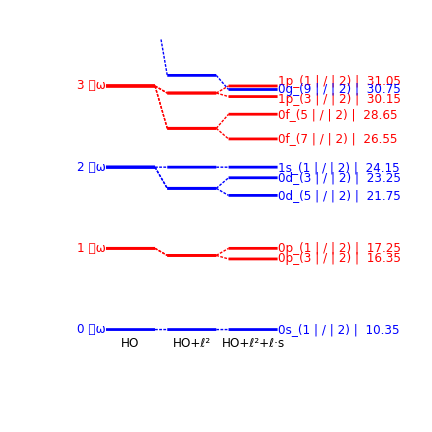

```mathematica
HOParams={6.9,-0.3,-0.6};
HOParams0=HOParams*{1,0,0};
HOParams1=HOParams*{1,1,0};
HOParams2=HOParams*{1,1,1};
Figure[
{

SetOptions[Lev,Thickness->2],
SetOptions[Connector,Dashing->2],
SetOrigin[0],
Table[
Lev[0,1,ESM[HOParams0,nlj],
Color->ShellColor[nlj],Tag->lev[{nlj,0}],
OffsetL->{+1,0},
Switch[
nlj,
{0,l_,j_}/;(j==l+1/2),LabL->Row[{nlj[[2]]," ω"}],
_,{}
]
],
{nlj,PlotLevelSet}
],

SetOrigin[1],
Table[
{
Lev[0,1,ESM[HOParams1,nlj],Color->ShellColor[nlj],Tag->lev[{nlj,1}]],
Connector[lev[{nlj,0}],lev[{nlj,1}],Color->ShellColor[nlj]]
},
{nlj,PlotLevelSet}
],

SetOrigin[2],
Table[
{
Lev[0,1,ESM[HOParams2,nlj],
Color->ShellColor[nlj],Tag->lev[{nlj,2}],
LabR->Grid[{{ShellLabel[nlj],FixedPointForm[ESM[HOParams2,nlj],2]}},ItemSize->3,Spacings->0],
OffsetR->{-1,0},
(* special adjustments *)
Switch[
nlj,
{1,1,3/2},{NudgeC->-3,NudgeR->-3},
{1,1,1/2},{NudgeC->+6,NudgeR->+6},
_,{}
]
],
Connector[lev[{nlj,1}],lev[{nlj,2}],Color->ShellColor[nlj]]
},
{nlj,PlotLevelSet}
],

SetOptions[BandLabel,Offset->{0,-1},Nudge->-25],  (* align bottoms rather than top of subscript *)
BandLabel[lev[{{0,0,1/2},0}],"HO"],
BandLabel[lev[{{0,0,1/2},1}],Row[{"HO+",Superscript[textbf["ℓ"],2]}]],
BandLabel[lev[{{0,0,1/2},2}],Row[{"HO+",Superscript[textbf["ℓ"],2],"+",textbf["ℓ"],"·",textbf["s"]}]],

},
PlotRange->{{-1,4},{5,35}},
ImageSize->72*{6,6}
]
```

## Molecular potentials and spectra: Combining plots and level schemes in one figure

This figure illustrates several possibilities for drawing a figure:

	1. Creating multipanel plots with unequal panel sizes, gaps between panels, and colored frames
	
	2. Including functions in a plot, and controlling their appearance by changing the default options (here Thickness) for RawGraphics
	
	3. Drawing axes with SchemeAxis
	
	4. Annotating plots with drawing objects, here SchemeCircle
	
	5. Defining functions (here U2Lev and SO3Lev) to draw levels based on energy formulas
	
	6. Using Table to construct level schemes with many levels automatically

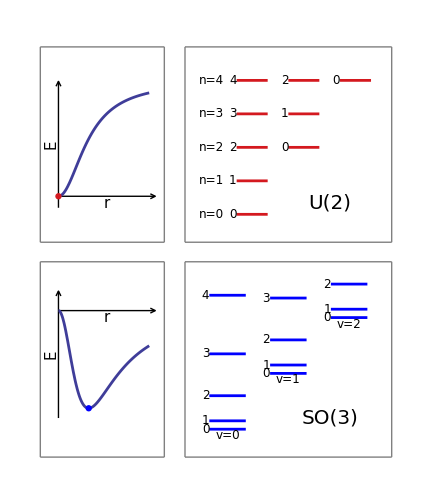

```mathematica
U2Lev[k_,n_]:=Lev[lev[k,n],k,k+1,epsilon*n,LabL->n-2*k];
SO3Lev[v_,l_]:=Lev[lev[v,l],v,v+1,v+b*l^2,LabL->l];

scrE=textit["E"];
(* MS Windows users -- try using this definition for a fancy script E:
scrE=textbf[textfamily["Script","E"]];   
*)

Figure[
{

(* set up drawing options *)

SetOptions[SchemeObject,FontFamily->"Times New Roman"],
SetOptions[ScaledLabel,FontSize->20],
SetOptions[Lev,OffsetL->{+1,0},Thickness->2,Margin->0.2,WingTipWidth->10,WingRiseWidth->5],
SetOptions[Trans,HeadLength->5,HeadLip->2,Thickness->1.5],
SetOptions[RawGraphics,Thickness->2],
SetOptions[SchemeAxis,FontSize->15],

(* set up multipanel plot *)

Multipanel[
{{0,1},{0,1}},
{2,2},
XPanelSizes->{0.6,1},
XGapSizes->0.1,
YGapSizes->0.1,
ShowPanelLetter->False,
Frame->True,LineColor->Gray,ShowTicks->{False,False,False,False},
Margin->1
],

(* draw functions *)

FigurePanel[{1,1},XPlotRange->{-0.6,3.5},YPlotRange->{-0.4,1.3}],
SchemeAxis[Left,0,{-0.1,1},LabL->scrE],
SchemeAxis[Bottom,{0,3.2},0,LabB->textit["r"]],
RawGraphics[Plot[(1+r^2)^(-1)*r^2,{r,0,3}]],
SchemeCircle[{0,0},Point[3],Color->VenetianRed],

FigurePanel[{2,1},XPlotRange->{-0.6,3.5},YPlotRange->{-1.5,0.5}],
SchemeAxis[Left,0,{-1.1,0.2},LabL->scrE],
SchemeAxis[Bottom,{0,3.2},0,LabB->textit["r"]],
RawGraphics[Plot[-4*(1+r^2)^(-2)*r^2,{r,0,3}]],
SchemeCircle[{1,-1},Point[3],Color->Blue],

(* draw level schemes *)

FigurePanel[{1,2},XPlotRange->{-0.8,3.2},YPlotRange->{-0.5,3}],
SetOptions[Lev,LineColor->VenetianRed],
epsilon=0.6,
Table[U2Lev[k,n],{k,0,2},{n,2*k,4}],
Table[LevelLabel[lev[0,n],Left,RowBox[{textit["n"],"=",n}],Gap->15],{n,0,4}],
ScaledLabel[{0.7,0.2},"U(2)"],

FigurePanel[{2,2},XPlotRange->{-0.2,3.2},YPlotRange->{-0.5,3}],
SetOptions[Lev,LineColor->Blue],
b=0.15,
Table[SO3Lev[0,l],{l,0,4}],
Table[SO3Lev[1,l],{l,0,3}],
Table[SO3Lev[2,l],{l,0,2}],
Table[BandLabel[lev[v,0],RowBox[{textit["v"],"=",v}]],{v,0,2}],
ScaledLabel[{0.7,0.2},"SO(3)"],

},
PlotRange->{{0,1},{0,1}},
Frame->False,ImageSize->72*{6,7}
]
```

## LevelScheme poster (original)

This illustrates the use of the Table function to automatically generate sets of levels.

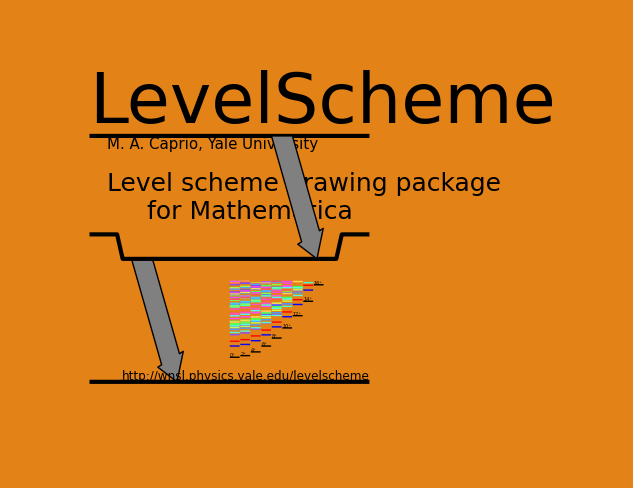

```mathematica
RotationalBand[Name_,BandHead_,Moment_,MaxSpin_,MaxEnergy_,ShowLab_,Col_]:=
Table[
Energy=Moment*J*(J+1)+BandHead;
If[Energy≤MaxEnergy,
LevelE[Name][J]=Energy;
Lev[BandMember[Name][J],J/2*0.03,(J/2+1)*0.03,Energy,LabL->SuperscriptBox[J,"+"],ShowLabL->ShowLab,Color->Col]
],
{J,0,MaxSpin,2}];
Figure[{
SetOptions[Lev,Thickness->3,WingTipWidth->50],
SetOptions[Trans,ArrowType->ShapeArrow,FillColor->Gray,Width->35,HeadLength->30,HeadLip->7.5],

Lev[Lev3,0,1,200,LabL->RowBox[{textit["LevelScheme"]}],FontSize->70],
SchemeIfDef["Streamlined",
SetOptions[Lev,ShowLabL->False,ShowLabR->False],
SetOptions[Lab,ShowText->False]
],
Lev[Lev2,0,1,100,WingHeight->30],
Lev[Lev1,0,1,0,LabR->texttt["http://wnsl.physics.yale.edu/levelscheme"],OffsetR->{1,-1.1}],
ManualLabel[{0.15,150},StackText[Left,0,{"Level scheme drawing package","     for Mathematica"}],
FontSize->25,Offset->{-1,0}],
ManualLabel[{0.15,200},
"M. A. Caprio, Yale University",FontSize->15,
Offset->{-1,1}],

Trans[Lev3,0.65,Lev2,0.75],
Trans[Lev2,0.25,Lev1,0.35],

(* Generate levels for mini-scheme *)

SetOptions[Lev,Thickness->1,Margin->0.001,FontSize->5],
 
SetScale[0.013];
SetOrigin[{0.5,20}];
MaxSpin=16;
MaxEnergy=4800;
RotationalBand[0,0,N[100/6],MaxSpin,MaxEnergy,True,Black],
RotationalBand[1,700,N[100/6],MaxSpin,MaxEnergy,False,Blue],
RotationalBand[2,1000,N[100/6],MaxSpin,MaxEnergy,False,Red],
SeedRandom[0],
Table[
RotationalBand[Dummy,Random[Real,{1300,MaxEnergy}],N[100/6]*Random[Real,{0.8,1.2}],MaxSpin,MaxEnergy,False,Hue[Random[],0.7,1]],
{50}
]
},
PlotRange->{{0,1},{-50,275}},ImageSize->72*0.8*{11,8.5},Background->YellowOchre]
```

## LevelScheme poster (revised)

This illustrates the use of the Table function to automatically generate sets of levels.

Caveat: LevelScheme's data plotting capability (DataPlot), used in this poster, is still under development.  If you decide to use it, be aware that the syntax is subject to change in future versions of LevelScheme.  Note that Mathematica's usual data plotting functions (ListPlot, etc.) can always be used to generate data plots within LevelScheme figures.

Caveat: Since this example uses object transparency (the Opacity option), PostScript or EncapsulatedPostscript export may not work well and may even crash Mathematica.

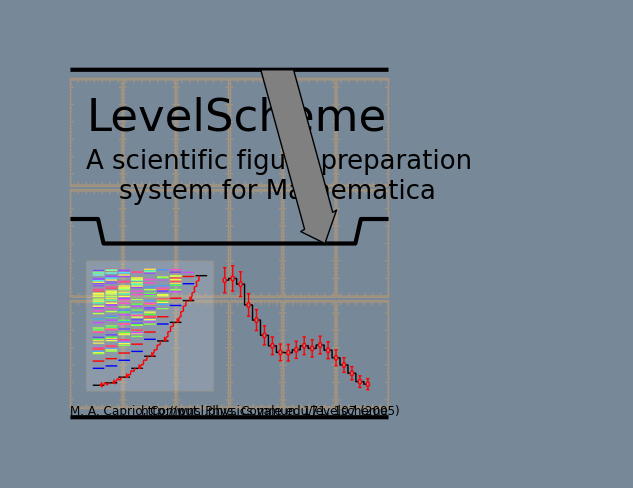

```mathematica
WData=Replace[
{{{180,2095},ErrorBar[45]},{{175,2124},ErrorBar[45]},{{170,2030},ErrorBar[44]},{{165,1691},ErrorBar[40]},{{160,1444},ErrorBar[37]},{{155,1195},ErrorBar[34]},{{150,1024},ErrorBar[31]},{{145,917},ErrorBar[30]},{{140,911},ErrorBar[30]},{{135,959},ErrorBar[30]},{{130,1025},ErrorBar[31]},{{125,982},ErrorBar[31]},{{120,1037},ErrorBar[32]},{{115,952},ErrorBar[30]},{{110,828},ErrorBar[28]},{{105,711},ErrorBar[26]},{{100,576},ErrorBar[24]},{{95,439},ErrorBar[21]},{{90,398},ErrorBar[20]}},
{{theta_,value_},ErrorBar[err_]}:>{180-theta,ErrorValue[value/898.1,Sqrt[value/898.1]*0.15]},{1}
];
Figure[{

SetOptions[Lev,Thickness->3,WingTipWidth->50,Margin->0],
Lev[Lev3,0,1,200],
Lev[Lev2,0,1,100,WingHeight->30],
Lev[Lev1,0,1,0],

ManualLabel[{0.05,185},"LevelScheme",FontSize->45,FontSlant->"Italic",Offset->{-1,+1}],
ManualLabel[{0.05,155},StackText[Left,0.2,
{
"  A scientific figure preparation",
"    system for Mathematica"
}
],FontSize->26,Offset->{-1,+1}],

ManualLabel[{0,0},Row[{"M. A. Caprio, Comput. Phys. Commun. ",textbf["171"],", 107 (2005)"}],Offset->{-1,-1.1}],
ManualLabel[{1,0},texttt["http://wnsl.physics.yale.edu/levelscheme"],Offset->{1,-1.1}],


SetOptions[Trans,ArrowType->ShapeArrow,FillColor->Gray,Width->55,HeadLength->30,HeadLip->7.5],
Trans[Lev3,0.65,Lev2,0.80],
(*Trans[Lev2,0.25,Lev1,0.35],*)

Multipanel[
{{0,1},{0+5,200-5}},
{3,6},
LineColor->Beige,
ShowPanelLetter->False,
XGapSizes->0.03,
YGapSizes->0.03,
ShowTickLabelsExterior->{False,False,False,False},
Layer->-1
],
Table[FigurePanel[{i,j}],{i,1,3},{j,1,6}],

SetOptions[FigurePanel,Frame->False],
FigurePanel[{{0.46,0.96},{5,100}},PlotRange->{{-5,90+5},{0,3}}],
SetOptions[DataLine,LineShape->"Step"],
SetOptions[DataSymbol,FillColor->LightSlateGray,Color->Red,SymbolSize->6],
DataPlot[WData],

SetOptions[FigurePanel,Frame->True,FrameTicks->None,Color->Beige,Opacity->0.4,Background->White,BackgroundOpacity->0.15,ExtendRange->0.05],
FigurePanel[{{0.05,0.45},{15,90}},PlotRange->{{0,9},{0,5000-100}}],
SetOptions[Lev,Thickness->1,Margin->0.05,FontSize->7],
DrawBand[Name_,BandHead_,Moment_,MaxSpin_,MaxEnergy_,ShowLab_,Col_]:=
Table[
Energy=Moment*J*(J+1)+BandHead;
If[Energy≤MaxEnergy,
LevelE[Name][J]=Energy;
Lev[BandMember[Name][J],J/2,(J/2+1),Energy,LabL->SuperscriptBox[J,"+"],ShowLabL->ShowLab,Color->Col]
],
{J,0,MaxSpin,2}];
MaxSpin=16;
MaxEnergy=4800;
DrawBand[0,0,N[100/6],MaxSpin,MaxEnergy,True;False,Black],
DrawBand[1,700,N[100/6],MaxSpin,MaxEnergy,False,Blue],
DrawBand[2,1000,N[100/6],MaxSpin,MaxEnergy,False,Red],
SetOptions[Trans,ArrowType->SquiggleArrow,Color->Red,HeadLength->4,HeadLip->3,Width->3,SquiggleWavelength->8,SquiggleBuffer->2,SquiggleSide->Right,EndPositions->{0.37,0.63}],
(*Trans[BandMember[1][0],BandMember[0][0]],*)
Table[Trans[BandMember[0][J],BandMember[0][J-2]],{J,2,MaxSpin,2}],
SeedRandom[0],
Table[
DrawBand[Dummy,Random[Real,{1300,MaxEnergy}],N[100/6]*Random[Real,{0.8,1.2}],MaxSpin,MaxEnergy,False,GrayLevel[Random[]];Hue[Random[],0.7,1]],
{50}
]

},
PlotRange->{{-0.05,1.05},{-15,200+15}},ImageSize->72*0.8*{11,8.5},Background->LightSlateGray]
```